## Definitions

```mathematica
cM := 6.67;
cMStar := cM * .9;
cF := 1;
cFDelta := 1.7;
cWDelta := 2.1;
```

## Functions

### Building blocks 1

```mathematica
a[k_, w_] := w - k ^ 2 / (2 cM);
b[k_, pf_] := k pf / cM;
w0[k_] := Sqrt[k ^ 2 + 1];
wDelta[k_] := cWDelta + k ^ 2 / (2 cM);
n0[pf_] := pf ^ 3 / (6 Pi ^ 2);
```

### Building blocks 2

```mathematica
phi0[k_, w_, pf_] := (cM / k) ^ 3 / (4 Pi ^ 2) ((a[k, w] ^ 2 - b[k, pf] ^ 2) / 2 Log[(a[k, w] + b[k, pf]) / (a[k, w] - b[k, pf])] - a[k, w] b[k, pf]);
phi[k_, w_, pf_] := phi0[k, w, pf] + phi0[-k, -w, pf];
phiDelta[k_, w_, pf_] := phi0[k, w - cWDelta, pf] + phi0[-k, -w - cWDelta, pf];

phi0Dw[k_, w_, pf_] := (cM / k) ^ 3 / (4 Pi ^ 2) (a[k, w] Log[(a[k, w] + b[k, pf]) / (a[k, w] - b[k, pf])] - 2 b[k, pf])
phiDw[k_, w_, pf_] := -n0[pf] / a[k, w]
```

## Playground

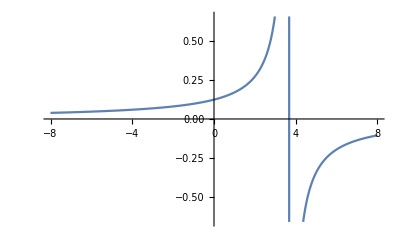

```mathematica
Plot[Re[phiDw[7, w, 3]], {w, -8, 8}, Exclusions->None]
```